```mathematica
Exit[]
```

```mathematica
$Assumptions=μ>0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
```

```mathematica
t == σ √T; mpr==(μ-r)/σ^2;ost=.
xx[W_,mpr_,t_]:=Exp[ t W+(mpr-1/2)t^2];
put[k_,t_]:=BlackScholesPut[1,k,1,0,t,0]
```

```mathematica
γ=.1;mpr=0.1;t=1;
NIntegrate[Max[0,1.1-xx[w,0,.1]]Exp[-w^2/2],{w,-∞,∞}]/√(2π)-put[1.1,.1]

pr[a_,k_]:=-Log[NIntegrate[Exp[-a Max[0,k-xx[w,mpr,t]]-w^2/2],{w,-∞,∞}]/√(2π)]-a put[k,t];
pr2[a_,k_]:=NIntegrate[Exp[-a (Max[0,k-xx[w,mpr,t]]-put[k,t])-w^2/2] (Max[0,k-xx[w,mpr,t]]-put[k,t]),{w,-∞,∞}];
```

-5.88141×10^-14

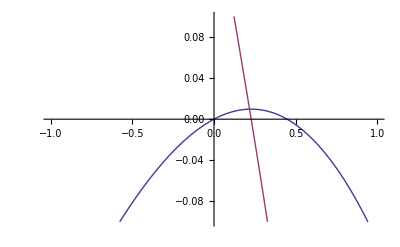

```mathematica
mpr=-.15;Plot[{pr[a,2],pr2[a,2]},{a,-1,1},PlotRange-> {-.1,.1}]
```

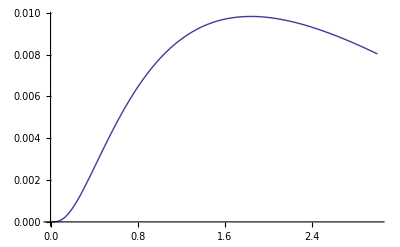

```mathematica
mpr=-.15;Plot[{pr[.23,k]},{k,0,3}]
```

```mathematica
Quiet[FindRoot[pr2[a,1.9]==0,{a,-1,1}]]
```

{a→0.23679}

```mathematica
Plot3D[pr[a,k],{a,-1,1},{k,0,3},PlotRange->{-.2,.2}]
```

```mathematica
Normal[Series[df[a,w, 0,t],{t,0,3}]]
```

-ⅇ^(-w^2/2) t w+1/2 ⅇ^(-w^2/2) t^2 (1-2 mpr-w^2+2 a w^2)-1/6 ⅇ^(-w^2/2) t^3 w (-3+6 a+6 mpr-12 a mpr+w^2-6 a w^2+3 a^2 w^2)

```mathematica
Integrate[,{w,-∞,∞}]
```

√(π/2) (2+a t (2 b+3 (-1+a) b^2 t+(a-2 mpr) t))

```mathematica
MinValue[√(π/2) (2+a t (2 b+3 (-1+a) b^2 t+(a-2 mpr) t)),{a}]
```

Piecewise[{{√(2 π), (b>0&&t==0)||(b<0&&t==0)}, {1/4 (4 √(2 π)-2 mpr^2 √(2 π) t^2), b==0}, {1/(4+12 b^2)(4 √(2 π)+10 b^2 √(2 π)+6 b^3 √(2 π) t+4 b mpr √(2 π) t-9 b^4 √(π/2) t^2-6 b^2 mpr √(2 π) t^2-2 mpr^2 √(2 π) t^2), True}}]

```mathematica
Series[%,{t,0,2}]
```

√(2 π)+a b √(2 π) t+(a^2-3 a b^2+3 a^2 b^2-2 a mpr) √(π/2) t^2+O[t]^3

```mathematica
Integrate[SeriesCoefficient[df[a,w, b √t,t],{t,0,2}],{w,-∞,∞}]
```

1/4 (8 a+35 (-1+2 (-1+a) a (-7+2 a)) b^4-8 mpr) √(π/2)

```mathematica
SeriesCoefficient[df[a,w, b,t],{t,0,2}]
```

a ⅇ^(a (1-ⅇ^(-2.4 w^2))-5.3 w^2) w^2-1/2 ⅇ^(a (1-ⅇ^(-2.4 w^2))-2.9 w^2) (-1+2 mpr+w^2)+1/2 ⅇ^(a (1-ⅇ^(-2.4 w^2))-w^2/2) (1-ⅇ^(-2.4 w^2)) (a^2 ⅇ^(-4.8 w^2) w^2-a ⅇ^(-2.4 w^2) (-1+2 mpr+w^2))

```mathematica
1/2 (-1+2 a) ⅇ^(-w^2/2) t^2 w^2-1/6 (1-6 a+3 a^2) ⅇ^(-w^2/2) t^3 w^3
```

1/2 (-1+2 a) ⅇ^(-w^2/2) t^2 w^2-1/6 (1-6 a+3 a^2) ⅇ^(-w^2/2) t^3 w^3

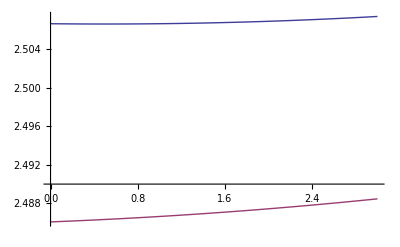

```mathematica
ost=.01;mpr=0.5;b=2.4;o=-0 3;p=3;Plot[{g[Max[0,a],∞],g[a,b]},{a,o,p}]
```

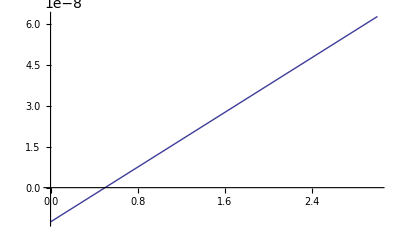

```mathematica
ost=.0001;b=2.4;o=-1 0;p=3;Plot[{dg[Max[0,a],∞]},{a,o,p}]
```

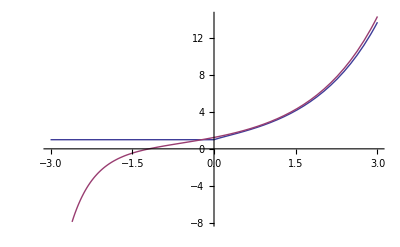

```mathematica
b=.1;o=-3;p=3;Plot[{dg[Max[0,a],0],dg[a,b]},{a,o,p}]
```

```mathematica
h[b_]:=Quiet[FindRoot[dg[a,b]==0,{a,-5,5}][[1,2]]]
```

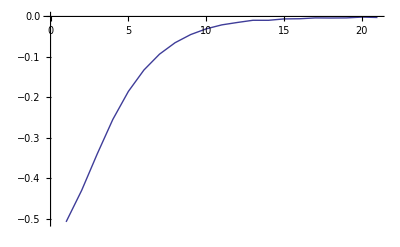

```mathematica
ListLinePlot[Table[h[1/n/2],{n,10,30}]]
```

```mathematica
fcs=Quiet[Table[fc2[n],{n,650}]];
```

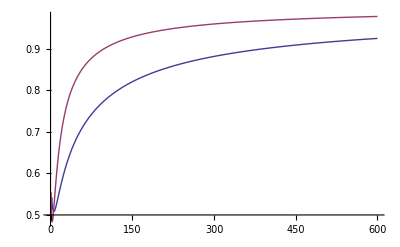

```mathematica
ListLinePlot[Transpose[Table[{Abs[fcs[[n]]]^(1/n),Abs[fcs[[n+1]]/fcs[[n]]]},{n,1,600}]]]
```